```mathematica
generate[n_,p_]:=Module[
{mat,deg,row,col,rand},
{
mat=Table[0,{i,1,n},{j,1,n}];
deg=Table[0,{i,1,n}];
For[
row=1,
row<n,
row++,
{
For[
col=row+1,
col≤n,
col++,
{
rand=RandomReal[{0,1}];
If[
rand≤p,
{
mat[[row]][[col]]=1;
mat[[col]][[row]]=1;
deg[[row]]++;
deg[[col]]++;
}
]
}
]
}
]
};
{mat,deg}
]
```

```mathematica
{a,deg}=generate[400,0.01];
```

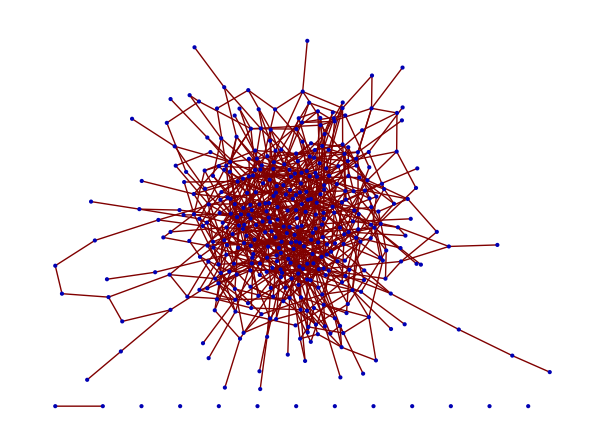

```mathematica
GraphPlot[a]
```

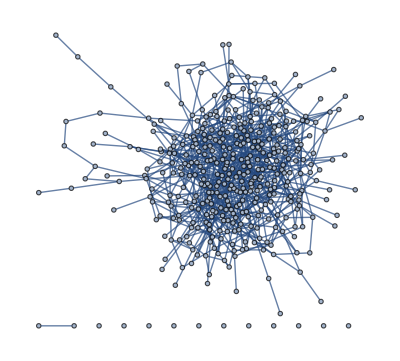

```mathematica
g=AdjacencyGraph[a]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

```mathematica
Sum[VertexDegree[g][[i]],{i,1,Length[VertexDegree[g]]}]
```

1584

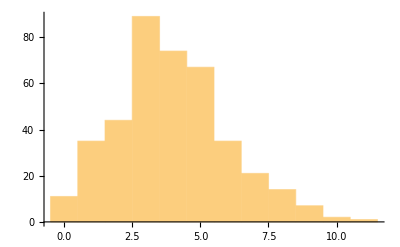

```mathematica
Histogram[VertexDegree[g],20]
```

```mathematica
N[GraphAssortativity[g]]
```

0.0279562

```mathematica
pCon=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLoss=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLossB=Table[Power[(deg[[i]]+1),-1],{i,1,Length[deg]}];
pPrune=Table[Power[(deg[[i]]+1),-2],{i,1,Length[deg]}];
cCon=Table[N[Sum[pCon[[i]],{i,1,j}]],{j,1,Length[pCon]}];
cLoss=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cLossB=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cPrune=Table[N[Sum[pPrune[[i]],{i,1,j}]],{j,1,Length[pPrune]}];
```

```mathematica
NIter=1000;
NPrun=10;
NGen=1;
NTry=25;
```

```mathematica
For[
iter=1,
iter≤NIter,
iter++,
Print[iter];
If[
Mod[iter,NGen]==0,
{
reConA=RandomReal[{0,cCon[[Length[cCon]]]}];

reNa=1;
While[
cCon[[reNa]]<reConA,
reNa++
];
reConB=RandomReal[{0,cLoss[[Length[cLoss]]]}];
reNb=1;
While[
cLoss[[reNb]]<reConB,
reNb++
];
try=0;
While[
( reNa==reNb || a[[reNa]][[reNb]]==1) && try<NTry,
{
try++;
reConB=RandomReal[{0,cLoss[[Length[cLoss]]]}];
reNb=1;
While[
cLoss[[reNb]]<reConB,
reNb++
]
}
];
If[
try<NTry ||(reNa≠reNb && a[[reNa]][[reNb]]==0),
{
a[[reNa]][[reNb]]=1;
a[[reNb]][[reNa]]=1;
deg[[reNa]]++;
deg[[reNb]]++;
}
];
try=0;
pCon=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLoss=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLossB=Table[Power[(deg[[i]]+1),-1],{i,1,Length[deg]}];
pPrune=Table[Power[(deg[[i]]+1),-2],{i,1,Length[deg]}];
cCon=Table[N[Sum[pCon[[i]],{i,1,j}]],{j,1,Length[pCon]}];
cLoss=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cLossB=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cPrune=Table[N[Sum[pPrune[[i]],{i,1,j}]],{j,1,Length[pPrune]}];
}
];
reConA=RandomReal[{0,cCon[[Length[cCon]]]}];
reNa=1;
While[
cCon[[reNa]]<reConA,
reNa++
];
reConB=RandomReal[{0,cLoss[[Length[cLoss]]]}];
reNb=1;
While[
cLoss[[reNb]]<reConB,
reNb++
];
try=0;
While[
(reNa==reNb || a[[reNa]][[reNb]]==1)&& try<NTry,
{
try++;
reConB=RandomReal[{0,cLoss[[Length[cLoss]]]}];
reNb=1;
While[
cLoss[[reNb]]<reConB,
reNb++
]
}
];
If[
try<NTry ||(reNa≠reNb && a[[reNa]][[reNb]]==0) ,
{
a[[reNa]][[reNb]]=1;
a[[reNb]][[reNa]]=1;
deg[[reNa]]++;
deg[[reNb]]++;
}
];
try=0;
reConC=RandomReal[{0,cLossB[[Length[cLossB]]]}];
reNc=1;
While[
cLossB[[reNc]]<reConC,
reNc++
];
While[
(reNc==reNa || reNc==reNb || a[[reNb]][[reNc]]==0)&& try<NTry,
{
try++;
reConC=RandomReal[{0,cLossB[[Length[cLossB]]]}];
reNc=1;
While[
cLossB[[reNc]]<reConC,
reNc++
]
}
];
If[
try<NTry  || (reNc≠ reNa && reNc≠ reNb && a[[reNb]][[reNc]]==1),
{
a[[reNb]][[reNc]]=0;
a[[reNc]][[reNb]]=0;
deg[[reNb]]--;
deg[[reNc]]--;
}
];
try=0;
pCon=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLoss=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLossB=Table[Power[(deg[[i]]+1),-1],{i,1,Length[deg]}];
pPrune=Table[Power[(deg[[i]]+1),-2],{i,1,Length[deg]}];
cCon=Table[N[Sum[pCon[[i]],{i,1,j}]],{j,1,Length[pCon]}];
cLoss=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cLossB=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cPrune=Table[N[Sum[pPrune[[i]],{i,1,j}]],{j,1,Length[pPrune]}];
If[
Mod[iter,NPrun]==0,
{
Prun=RandomReal[{0,cPrune[[Length[cPrune]]]}];
pr=1;
While[
cPrune[[pr]]<Prun,
pr++
];
a1=Table[0,{i,1,Length[a]-1},{j,1,Length[a]-1}];
deg1=Table[0,{i,1,Length[deg]-1}];
For[
row=1,
row≤Length[a],
row++,
{
For[
col=1,
col≤Length[a],
col++,
{
If[
row<pr && col <pr,
a1[[row]][[col]]=a[[row]][[col]],
{
If[
row>pr && col<pr,
a1[[row-1]][[col]]=a[[row]][[col]],
{
If[
row<pr && col>pr,
a1[[row]][[col-1]]=a[[row]][[col]],
{
If[
row>pr && col>pr,
a1[[row-1]][[col-1]]=a[[row]][[col]]
]
}
]
}
]
}
]
}
]
}
];
For[
d=1,
d≤Length[deg],
d++,
{
If[
d<pr,
deg1[[d]]=deg[[d]],
{
If[
d>pr,
deg1[[d-1]]=deg[[d]]
]
}
]
}
];
a=a1;
deg=deg1;
pCon=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLoss=Table[Power[(deg[[i]]+1),2],{i,1,Length[deg]}];
pLossB=Table[Power[(deg[[i]]+1),-1],{i,1,Length[deg]}];
pPrune=Table[Power[(deg[[i]]+1),-2],{i,1,Length[deg]}];
cCon=Table[N[Sum[pCon[[i]],{i,1,j}]],{j,1,Length[pCon]}];
cLoss=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cLossB=Table[N[Sum[pLoss[[i]],{i,1,j}]],{j,1,Length[pLoss]}];
cPrune=Table[N[Sum[pPrune[[i]],{i,1,j}]],{j,1,Length[pPrune]}];
}
];
]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

502

503

504

505

506

507

508

509

510

511

512

513

514

515

516

517

518

519

520

521

522

523

524

525

526

527

528

529

530

531

532

533

534

535

536

537

538

539

540

541

542

543

544

545

546

547

548

549

550

551

552

553

554

555

556

557

558

559

560

561

562

563

564

565

566

567

568

569

570

571

572

573

574

575

576

577

578

579

580

581

582

583

584

585

586

587

588

589

590

591

592

593

594

595

596

597

598

599

600

601

602

603

604

605

606

607

608

609

610

611

612

613

614

615

616

617

618

619

620

621

622

623

624

625

626

627

628

629

630

631

632

633

634

635

636

637

638

639

640

641

642

643

644

645

646

647

648

649

650

651

652

653

654

655

656

657

658

659

660

661

662

663

664

665

666

667

668

669

670

671

672

673

674

675

676

677

678

679

680

681

682

683

684

685

686

687

688

689

690

691

692

693

694

695

696

697

698

699

700

701

702

703

704

705

706

707

708

709

710

711

712

713

714

715

716

717

718

719

720

721

722

723

724

725

726

727

728

729

730

731

732

733

734

735

736

737

738

739

740

741

742

743

744

745

746

747

748

749

750

751

752

753

754

755

756

757

758

759

760

761

762

763

764

765

766

767

768

769

770

771

772

773

774

775

776

777

778

779

780

781

782

783

784

785

786

787

788

789

790

791

792

793

794

795

796

797

798

799

800

801

802

803

804

805

806

807

808

809

810

811

812

813

814

815

816

817

818

819

820

821

822

823

824

825

826

827

828

829

830

831

832

833

834

835

836

837

838

839

840

841

842

843

844

845

846

847

848

849

850

851

852

853

854

855

856

857

858

859

860

861

862

863

864

865

866

867

868

869

870

871

872

873

874

875

876

877

878

879

880

881

882

883

884

885

886

887

888

889

890

891

892

893

894

895

896

897

898

899

900

901

902

903

904

905

906

907

908

909

910

911

912

913

914

915

916

917

918

919

920

921

922

923

924

925

926

927

928

929

930

931

932

933

934

935

936

937

938

939

940

941

942

943

944

945

946

947

948

949

950

951

952

953

954

955

956

957

958

959

960

961

962

963

964

965

966

967

968

969

970

971

972

973

974

975

976

977

978

979

980

981

982

983

984

985

986

987

988

989

990

991

992

993

994

995

996

997

998

999

1000

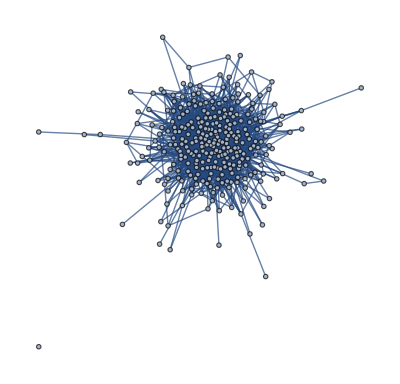

```mathematica
gg=AdjacencyGraph[a]
```

```mathematica
CommunityGraphPlot[gg]
```

-Graphics-

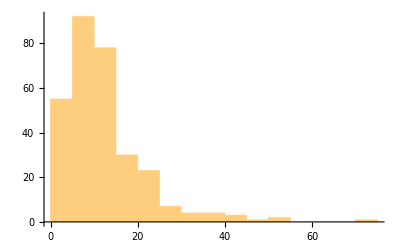

```mathematica
Histogram[VertexDegree[gg],20]
```

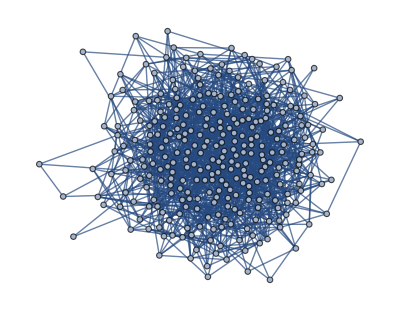

-Graphics-

```mathematica
g=AdjacencyGraph[a]
CommunityGraphPlot[g]
Histogram[VertexDegree[g],20]
```

```mathematica
N[GraphAssortativity[gg]]
```

-0.0840105

```mathematica
aa=VertexDegree[gg]
```

{3,20,6,13,20,10,6,20,17,8,20,12,5,7,1,14,3,14,3,4,25,15,9,9,11,10,17,2,21,30,10,5,12,12,12,42,24,1,14,8,8,9,6,19,3,23,11,4,9,38,6,3,23,9,27,5,17,13,10,12,7,21,7,41,7,4,13,15,22,6,9,14,9,13,13,9,2,13,8,2,5,5,8,19,18,21,5,11,37,6,5,22,18,6,11,4,51,8,1,10,5,1,18,10,7,3,20,8,11,6,8,14,16,12,18,4,7,15,5,8,25,6,6,3,7,12,6,11,11,18,7,3,6,12,70,18,13,3,15,7,31,5,16,7,2,9,11,11,11,6,14,6,28,7,14,20,18,17,18,13,29,25,9,4,32,13,5,9,9,13,1,7,6,3,13,21,14,3,6,2,7,5,2,7,14,15,24,12,2,2,13,2,4,2,17,12,11,10,8,5,37,13,2,15,45,3,2,9,6,19,11,9,2,3,4,2,13,20,10,14,8,4,10,7,38,10,1,7,16,5,50,5,15,9,13,5,5,5,21,12,10,5,11,10,5,1,10,2,4,12,5,8,6,6,13,10,2,12,32,4,4,6,12,9,7,5,24,18,3,12,20,13,13,43,25,11,13,1,1,3,17,7,11,9,5,9,4,12,14,9,13,0,11,21,24,4,18,15,10,22}

```mathematica
Sum[aa[[i]],{i,1,Length[aa]}]
```

3504

```mathematica
a1=0;
a2=0;
a3=0;
a4=0;
a5=0;
a6=0;
```

```mathematica
For[
i=1,
i≤Length[aa],
i++,
If[
aa[[i]]≥32,
a1++,
{
If[
aa[[i]]≥16,
a2++,
{
If[
aa[[i]]≥8,
a3++,
{
If[
aa[[i]]≥4,
a4++,
{
If[
aa[[i]]≥2,
a5++,
{
If[
aa[[i]]≥1,
a6++
]
}
]
}
]
}
]
}
]
}
]
]
```

```mathematica
a1
```

0

```mathematica
a2
```

183

```mathematica
a3
```

116

```mathematica
a4
```

0

```mathematica
a5
```

1

```mathematica
a6
```

0

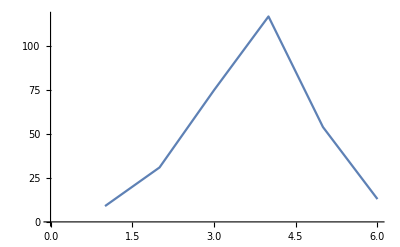

```mathematica
ListPlot[{a6,a5,a4,a3,a2,a1},Joined->True]
```

```mathematica
Length[a]
```

300

```mathematica
Count[VertexDegree[g]]
```

Count[{4,4,1,3,2,4,0,6,5,5,5,5,3,7,5,3,5,5,1,3,6,2,2,4,4,3,6,6,5,4,5,2,7,2,4,3,9,7,4,3,0,5,4,6,8,8,2,6,4,6,0,3,5,1,5,6,3,7,3,5,4,3,2,1,9,4,2,5,3,7,4,6,4,4,3,4,7,5,4,10,1,4,3,2,5,5,4,3,0,3,5,9,3,3,0,5,1,6,2,5,1,3,5,2,1,4,3,2,2,3,3,3,4,6,4,8,6,3,3,4,7,4,5,4,3,6,5,0,4,6,3,8,5,1,1,3,3,2,1,7,5,4,5,2,2,5,3,4,3,4,4,3,3,1,2,5,8,2,4,3,5,3,4,4,5,3,5,4,2,4,7,2,7,5,3,5,3,2,5,1,4,10,0,1,8,1,5,4,2,4,3,5,6,3,3,6,0,5,3,1,4,5,5,6,4,8,2,4,3,4,5,3,5,4,5,5,4,9,4,3,8,1,7,4,2,4,7,5,1,3,4,1,2,6,1,3,1,3,3,2,4,6,3,6,3,3,4,1,5,3,4,3,2,3,8,9,8,7,4,2,3,2,0,2,3,3,7,6,4,6,4,3,8,5,2,6,1,1,1,9,3,3,3,4,3,4,4,5,6,2,5,2,2,2,1,4,5,2,6,7,3,3,4,6,6,1,6,1,3,2,7,4,8,3,4,5,7,5,3,3,5,5,5,4,6,2,5,4,1,2,7,3,2,4,4,3,3,4,2,8,5,4,3,5,7,4,3,2,6,1,2,4,5,1,5,5,3,3,5,6,8,7,6,5,0,3,1,0,5,1,5,3,3,4,3,1,3,6,1,3,4,5,3,4,6,3,3,6,3,5,9,3,5,3,4,2,7,4,3,11}]

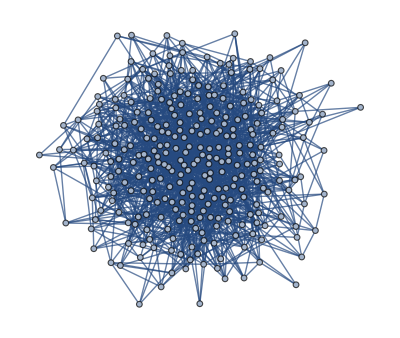

```mathematica
AdjacencyGraph[a]
```

```mathematica
CommunityGraphPlot[gg]
```

-Graphics-

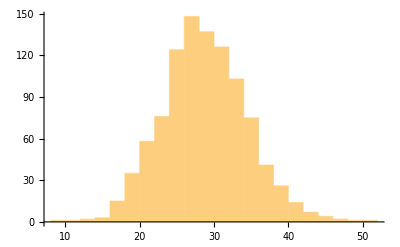

```mathematica
Histogram[VertexDegree[gg],20]
```

```mathematica
N[GraphAssortativity[gg]]
```

-0.0127098

```mathematica
aa=VertexDegree[gg]
```

{32,22,25,37,24,33,38,28,25,25,28,21,20,37,22,30,19,23,13,19,22,31,33,26,36,26,27,24,26,36,16,30,25,29,23,20,27,30,19,29,25,31,19,30,29,34,25,26,39,21,33,18,24,28,26,28,37,26,29,23,27,42,20,28,34,34,31,32,23,23,36,31,29,26,19,27,23,29,26,28,23,31,27,27,22,21,22,28,25,34,25,15,33,23,29,18,41,17,28,21,26,28,23,36,31,22,19,16,26,24,28,23,36,8,34,29,28,25,26,30,38,33,28,37,38,25,27,27,31,24,25,30,19,29,39,25,20,29,26,24,27,28,24,27,32,25,24,26,34,31,26,22,46,35,34,24,36,24,25,28,41,35,24,31,19,34,23,31,22,27,27,22,26,23,39,31,32,28,43,30,29,25,25,32,29,28,17,36,31,36,32,30,33,30,32,25,26,37,28,24,29,39,43,29,31,23,34,32,23,21,28,21,40,27,26,29,24,32,32,16,23,35,35,38,27,30,21,33,27,43,25,40,26,33,26,28,41,28,27,19,31,20,23,28,32,27,33,27,33,35,30,26,30,24,22,22,48,28,21,20,20,23,29,25,28,24,35,27,25,35,28,27,30,17,28,28,34,31,29,25,22,35,29,32,36,35,28,26,26,31,25,15,36,20,29,22,34,24,27,24,31,26,30,25,34,42,25,27,34,25,27,27,25,28,20,34,26,25,27,23,23,33,24,28,33,30,27,22,23,21,26,29,24,24,24,29,25,34,31,37,41,29,20,36,28,41,27,22,31,30,30,25,27,18,34,27,27,23,23,27,22,27,33,29,30,30,25,26,23,27,30,32,27,32,31,33,33,27,35,39,21,29,28,35,22,26,37,33,18,33,30,26,31,22,26,35,36,31,32,18,21,31,32,26,34,28,22,25,34,31,31,27,19,22,35,17,22,23,29,24,28,28,26,27,35,31,19,32,22,29,23,21,25,28,19,22,32,30,32,27,32,34,26,34,46,27,29,30,35,33,41,23,26,23,28,28,32,26,31,22,28,32,27,33,26,20,31,31,32,31,33,25,31,31,32,28,33,41,21,38,25,30,25,25,27,34,33,22,29,37,27,26,24,21,35,29,30,29,18,29,29,38,30,35,25,30,21,32,32,31,34,41,20,33,25,29,27,26,26,21,31,28,27,34,25,27,21,30,19,26,29,28,26,21,33,25,24,26,27,29,17,35,37,32,29,34,28,36,21,29,30,27,23,24,31,30,24,19,32,36,20,26,34,23,25,29,30,25,28,30,32,26,25,44,26,27,25,29,31,25,34,32,34,24,17,33,31,41,16,35,32,32,28,36,24,20,19,35,26,29,16,30,30,33,31,30,25,29,27,21,26,35,24,31,19,23,26,37,26,35,30,33,28,30,20,31,15,27,30,22,34,33,36,31,28,30,31,26,28,40,27,33,28,28,33,21,29,27,29,28,32,26,37,24,28,34,35,32,32,27,25,29,33,36,29,26,39,34,20,25,21,23,19,25,27,26,38,33,23,34,26,24,25,25,25,31,39,18,22,30,32,34,29,27,27,26,29,12,32,24,25,32,30,30,21,20,33,38,44,23,27,25,41,30,34,32,21,26,30,26,27,27,23,37,32,36,30,36,18,33,26,21,31,32,35,33,21,26,32,36,22,23,25,25,24,27,19,24,30,32,27,37,26,26,39,32,31,17,26,21,21,26,33,31,22,32,33,31,26,19,34,19,17,32,24,28,25,34,29,31,34,30,28,24,17,36,28,28,38,30,38,43,44,29,34,45,32,31,30,18,29,26,33,29,24,31,23,25,30,22,36,33,28,24,34,30,23,36,34,32,29,20,32,18,23,29,38,32,25,39,35,28,34,26,28,24,21,33,19,38,30,24,37,17,19,18,25,36,26,27,34,31,25,25,33,20,39,24,31,28,30,30,26,26,38,21,28,24,31,30,28,24,28,21,26,33,25,30,28,11,35,27,35,26,39,26,29,28,27,39,25,25,28,21,27,31,30,27,27,33,42,29,29,22,20,28,32,28,23,30,28,31,29,20,19,26,29,39,29,37,27,21,20,25,31,29,34,25,30,22,24,40,34,33,34,24,28,25,30,25,30,25,51,35,35,24,26,28,26,33,37,32,24,30,28,26,23,25,33,22,28,21,28,36,26,30,24,21,33,27,27,25,30,25,28,19,21,26,32,23,34,30,29,30,31,32,25,35,32,27,32,30,25,25,30,22,28,29,23,31}

```mathematica
Sum[aa[[i]],{i,1,Length[aa]}]
```

28262

```mathematica
a1=0;
a2=0;
a3=0;
a4=0;
a5=0;
a6=0;
```

```mathematica
For[
i=1,
i≤Length[aa],
i++,
If[
aa[[i]]≥32,
a1++,
{
If[
aa[[i]]≥16,
a2++,
{
If[
aa[[i]]≥8,
a3++,
{
If[
aa[[i]]≥4,
a4++,
{
If[
aa[[i]]≥2,
a5++,
{
If[
aa[[i]]≥1,
a6++
]
}
]
}
]
}
]
}
]
}
]
]
```

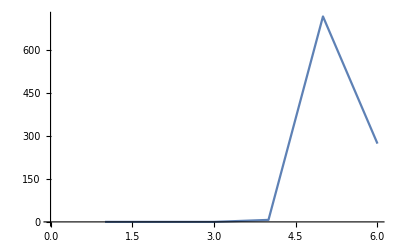

```mathematica
ListPlot[{a6,a5,a4,a3,a2,a1},Joined->True]
```